Computing densities for all p values...

Processing p = 100...

Processing p = 200...

Processing p = 300...

Processing p = 400...

Processing p = 500...

Processing p = 600...

Processing p = 700...

Processing p = 800...

Processing p = 1200...

Processing p = 1500...

Processing p = 3000...

Computing successive pointwise sup norms...

Exported plots:

C:\Users\b09335eb\Documents\RWIHS_Programmes_MATLAB\Working Versions\Probability Densities\Results\analytic_CPn_successive_convergence_n4_a0.100_k2_p100-3000_successive_supnorm.png

C:\Users\b09335eb\Documents\RWIHS_Programmes_MATLAB\Working Versions\Probability Densities\Results\analytic_CPn_successive_convergence_n4_a0.100_k2_p100-3000_integral_vs_p.png

C:\Users\b09335eb\Documents\RWIHS_Programmes_MATLAB\Working Versions\Probability Densities\Results\analytic_CPn_successive_convergence_n4_a0.100_k2_p100-3000_integral_error_vs_p.png

Displaying plots...

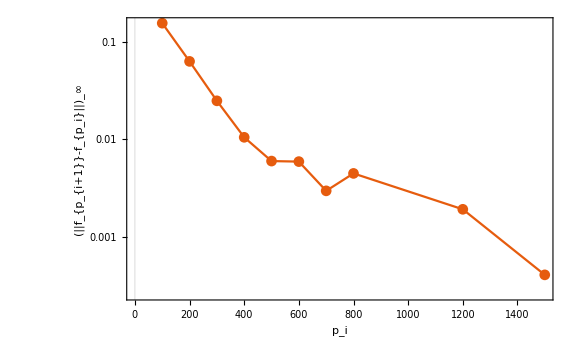

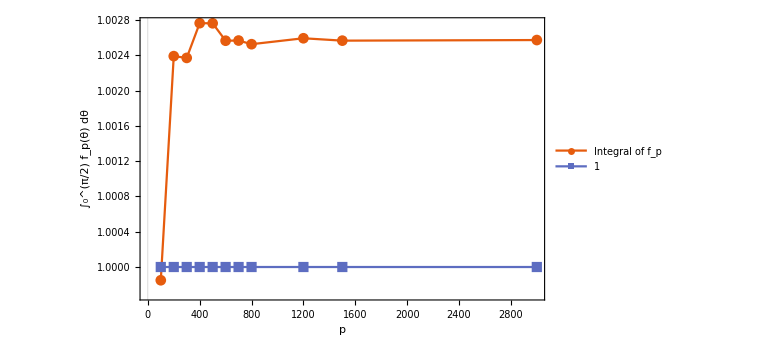

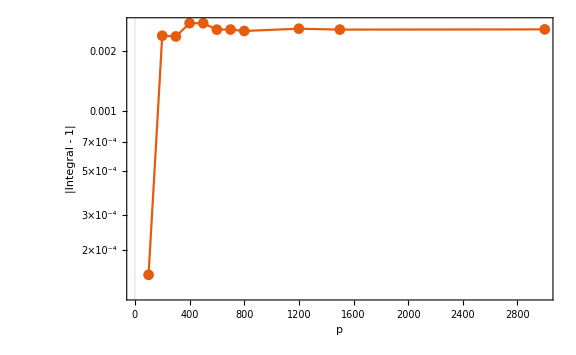

```mathematica
ClearAll["Global`*"];
$HistoryLength=0;

(*---------------------------------------------------------------*)
(*Parameters*)
(*---------------------------------------------------------------*)

n=2^2;
a=0.1;
k=2;

pList={100,200, 300, 400, 500, 600,700,800,1200,1500,3000};
NTheta=100;

thetaGrid=N@Subdivide[0,Pi/2,NTheta];
dTheta=thetaGrid[[2]]-thetaGrid[[1]];

exportDir=NotebookDirectory[]/. $Failed->Directory[];

aStr=StringReplace[ToString@NumberForm[a,{Infinity,3},NumberPadding->{"","0"}]," "->""];

outBase=FileNameJoin[{exportDir,"analytic_CPn_successive_convergence_n"<>ToString[n]<>"_a"<>aStr<>"_k"<>ToString[k]<>"_p"<>ToString[First[pList]]<>"-"<>ToString[Last[pList]]}];

(*---------------------------------------------------------------*)
(*Density on grid for truncation p*)
(*---------------------------------------------------------------*)

densityOnGrid[n_Integer,a_?NumericQ,k_Integer,p_Integer,grid_List]:=Module[{mVals,coeffs},mVals=Range[0,p];
coeffs=Table[(2 m+n-1) Binomial[m+n-2,n-2]*(JacobiP[m,n-2,0,Cos[2 a]]/JacobiP[m,n-2,0,1])^k,{m,mVals}];
Table[2 Sin[theta]^(2 n-3) Cos[theta]*Sum[coeffs[[m+1]]*JacobiP[m,n-2,0,Cos[2 theta]],{m,0,p}],{theta,grid}]]

(*---------------------------------------------------------------*)
(*Compute densities and integrals for each p*)
(*---------------------------------------------------------------*)

Print["Computing densities for all p values..."];

densityAssoc=Association[];
integralAssoc=Association[];

Do[Print["  Processing p = ",p,"..."];
densityAssoc[p]=N[densityOnGrid[n,a,k,p,thetaGrid]];
(*trapezoidal-rule integral*)integralAssoc[p]=Total[Most[densityAssoc[p]]+Rest[densityAssoc[p]]] dTheta/2;,{p,pList}];

(*---------------------------------------------------------------*)
(*Successive sup norms: ||f_{p_{i+1}}-f_{p_i}}||_∞*)
(*---------------------------------------------------------------*)

Print["Computing successive pointwise sup norms..."];

successiveMetrics=Table[Module[{p1,p2,diff,supNorm},p1=pList[[i]];
p2=pList[[i+1]];
diff=Abs[densityAssoc[p2]-densityAssoc[p1]];
supNorm=Max[diff];
{p1,p2,supNorm}],{i,1,Length[pList]-1}];

(*---------------------------------------------------------------*)
(*Integral table*)
(*---------------------------------------------------------------*)

integralMetrics=Table[{p,integralAssoc[p],Abs[integralAssoc[p]-1.0]},{p,pList}];

(*---------------------------------------------------------------*)
(*Export CSVs*)
(*---------------------------------------------------------------*)

(*successiveCSV=Prepend[successiveMetrics,{"p_i","p_{i+1}","SupNormDifference"}];

integralCSV=Prepend[integralMetrics,{"p","Integral","IntegralError"}];

Export[outBase<>"_successive_supnorm.csv",successiveCSV,"CSV"];
Export[outBase<>"_integrals.csv",integralCSV,"CSV"];

Print["Exported CSV files:"];
Print["  ",outBase<>"_successive_supnorm.csv"];
Print["  ",outBase<>"_integrals.csv"];*)
(*---------------------------------------------------------------*)
(*Plots*)
(*---------------------------------------------------------------*)

supNormData=successiveMetrics[[All,{1,3}]];
integralData=integralMetrics[[All,{1,2}]];
integralErrorData=integralMetrics[[All,{1,3}]];

supNormPlot=ListLogPlot[supNormData,Joined->True,Frame->True,FrameLabel->{"p_i","\!\(\*SubscriptBox[\(||f_{p_{i+1}}-f_{p_i}||\), \(∞\)]\)"},PlotMarkers->Automatic,ImageSize->Large,PlotTheme->"Scientific"];

integralPlot=ListLinePlot[{integralData,Table[{p,1.0},{p,pList}]},Joined->True,Frame->True,FrameLabel->{"p","\!\(\*SubsuperscriptBox[\(∫\), \(0\), \(π/2\)]\)f_p(θ) dθ"},PlotLegends->{"Integral of f_p","1"},PlotMarkers->Automatic,ImageSize->Large,PlotTheme->"Scientific"];

integralErrorPlot=ListLogPlot[integralErrorData,Joined->True,Frame->True,FrameLabel->{"p","|Integral - 1|"},PlotMarkers->Automatic,ImageSize->Large,PlotTheme->"Scientific"];

Export[outBase<>"_successive_supnorm.png",supNormPlot];
Export[outBase<>"_integral_vs_p.png",integralPlot];
Export[outBase<>"_integral_error_vs_p.png",integralErrorPlot];

Print["Exported plots:"];
Print["  ",outBase<>"_successive_supnorm.png"];
Print["  ",outBase<>"_integral_vs_p.png"];
Print["  ",outBase<>"_integral_error_vs_p.png"];

Print["Displaying plots..."];
Print[supNormPlot];
Print[integralPlot];
Print[integralErrorPlot];
```